```mathematica
f[kx_,ky_]:=Sqrt[1+4Cos[(√3 a)/2 kx]Cos[a/2 ky]+4(Cos^2)[a/2 ky]]
γ0 = 3.033
s0 = 0.129
e1[kx_,ky_]:= (γ0*f[kx,ky])/(1-s0*f[kx,ky])
e2[kx_,ky_]:= (-γ0*f[kx,ky])/(1+s0*f[kx,ky])
```

3.033

0.129

```mathematica
f[kx_,ky_]:=Sqrt[1+4 Cos[(Sqrt[3] a)/2 kx] Cos[a/2 ky]+4 (Cos[a/2 ky])^2]
```

```mathematica
fx = D[f[kx, ky], kx]
fy = D[f[kx, ky], ky]
```

-(√3 a Cos[(a ky)/2] Sin[1/2 √3 a kx])/(√(1+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+4 Cos[(a ky)/2]^2))

(-2 a Cos[1/2 √3 a kx] Sin[(a ky)/2]-4 a Cos[(a ky)/2] Sin[(a ky)/2])/(2 √(1+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+4 Cos[(a ky)/2]^2))

```mathematica
grad={fx,fy}
```

{-(√3 Cos[ky/2] Sin[(√3 kx)/2])/(√(1+4 Cos[(√3 kx)/2] Cos[ky/2]+4 Cos[ky/2]^2)),(-2 Cos[(√3 kx)/2] Sin[ky/2]-4 Cos[ky/2] Sin[ky/2])/(2 √(1+4 Cos[(√3 kx)/2] Cos[ky/2]+4 Cos[ky/2]^2))}

```mathematica
zeros=Reduce[grad=={0,0},{kx,ky}]
```

(C[1]|C[2])∈ℤ&&(((kx==(2 (-π/2+2 π C[2]))/(√3)||kx==(2 (π/2+2 π C[2]))/(√3))&&(ky==-π+4 π C[1]||ky==π+4 π C[1]))||(kx==(4 π C[2])/(√3)&&(ky==4 π C[1]||ky==2 (π+2 π C[1])))||(kx==-(-2 π-4 π C[1])/(√3)&&(ky==4 π C[2]||ky==2 π+4 π C[2])))

```mathematica
points={{kx->0,ky->0},{kx->-(π/Sqrt[3]),ky->-π},{kx->-(π/Sqrt[3]),ky->π},{kx->π/Sqrt[3],ky->-π},{kx->π/Sqrt[3],ky->π}}

functionValues=f[kx,ky]/. points
```

{{kx→0,ky→0},{kx→-π/(√3),ky→-π},{kx→-π/(√3),ky→π},{kx→π/(√3),ky→-π},{kx→π/(√3),ky→π}}

{3,1,1,1,1}

-(√3 Cos[ky/2] Sin[(√3 kx)/2])/(√(1+4 Cos[(√3 kx)/2] Cos[ky/2]+4 Cos[ky/2]^2))

(-2 Cos[(√3 kx)/2] Sin[ky/2]-4 Cos[ky/2] Sin[ky/2])/(2 √(1+4 Cos[(√3 kx)/2] Cos[ky/2]+4 Cos[ky/2]^2))

```mathematica
J=dEdkx*dEdky
```

-(√3 Cos[ky/2] Sin[(√3 kx)/2] (-2 Cos[(√3 kx)/2] Sin[ky/2]-4 Cos[ky/2] Sin[ky/2]))/(2 (1+4 Cos[(√3 kx)/2] Cos[ky/2]+4 Cos[ky/2]^2))

```mathematica
Clear[a]
f[kx_,ky_]:=Sqrt[1+4 Cos[(Sqrt[3] a)/2 kx] Cos[a/2 ky]+4 (Cos[a/2 ky])^2]
dEdkx=D[f[kx,ky],kx]
dEdky=D[f[kx,ky],ky]
```

-(√3 a Cos[(a ky)/2] Sin[1/2 √3 a kx])/(√(1+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+4 Cos[(a ky)/2]^2))

(-2 a Cos[1/2 √3 a kx] Sin[(a ky)/2]-4 a Cos[(a ky)/2] Sin[(a ky)/2])/(2 √(1+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+4 Cos[(a ky)/2]^2))

```mathematica
Norm[{dEdkx,dEdky}]
```

√(3 Abs[(a Cos[(a ky)/2] Sin[1/2 √3 a kx])/(√(1+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+4 Cos[(a ky)/2]^2))]^2+1/4 Abs[(-2 a Cos[1/2 √3 a kx] Sin[(a ky)/2]-4 a Cos[(a ky)/2] Sin[(a ky)/2])/(√(1+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+4 Cos[(a ky)/2]^2))]^2)

```mathematica
Simplify[%86]
```

√(3 Abs[(a Cos[(a ky)/2] Sin[1/2 √3 a kx])/(√(3+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+2 Cos[a ky]))]^2+Abs[(a (Cos[1/2 √3 a kx]+2 Cos[(a ky)/2]) Sin[(a ky)/2])/(√(3+4 Cos[1/2 √3 a kx] Cos[(a ky)/2]+2 Cos[a ky]))]^2)

```mathematica
Simplify[3(Cos[(a* ky)/2] Sin[1/2 √3 a *kx])^2+((Cos[1/2 √3 a *kx]+2 Cos[(a* ky)/2]) Sin[(a *ky)/2])^2 3/4 (2 Cos[Sqrt[3]/2 a kx]-Cos[Sqrt[3] a kx] Cos[a ky]-Sqrt[3] Sin[Sqrt[3]/2 a kx] Sin[a ky])^2+3/4 (Cos[Sqrt[3]/2 a kx] Cos[a ky]-Sqrt[3] Sin[Sqrt[3]/2 a kx] Sin[a ky])^2-E^2]
```

-ⅇ^2+3 Cos[(a ky)/2]^2 Sin[1/2 √3 a kx]^2+3/4 (Cos[1/2 √3 a kx] Cos[a ky]-√3 Sin[1/2 √3 a kx] Sin[a ky])^2+3/4 (Cos[1/2 √3 a kx]+2 Cos[(a ky)/2])^2 Sin[(a ky)/2]^2 (-2 Cos[1/2 √3 a kx]+Cos[√3 a kx] Cos[a ky]+√3 Sin[1/2 √3 a kx] Sin[a ky])^2

```mathematica
Expand[3 Cos[(a ky)/2]^2 Sin[1/2 √3 a kx]^2+(Cos[1/2 √3 a kx]+2 Cos[(a ky)/2])^2 Sin[(a ky)/2]^2]
```

3 Cos[(a ky)/2]^2 Sin[1/2 √3 a kx]^2+Cos[1/2 √3 a kx]^2 Sin[(a ky)/2]^2+4 Cos[1/2 √3 a kx] Cos[(a ky)/2] Sin[(a ky)/2]^2+4 Cos[(a ky)/2]^2 Sin[(a ky)/2]^2

```mathematica
B=(+(6.62607015*10^-34/(2Pi))^2*3.26)/(1.602176634*10^-19*9.10938356*10^-31)
R=10.08*10^-120
V1 = 2.08
β2 = 2/3
ϕ[d_]:=-(B/d^2+(9R)/d^12+5β2*V1^2/B*d^2)
V2[d_]:=B/d^2
```

2.48411×10^-19

1.008×10^-119

2.08

2/3

```mathematica
-2.48×10^-19
```

1.008×10^-119

2.03

2/3

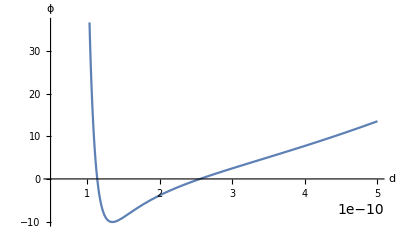

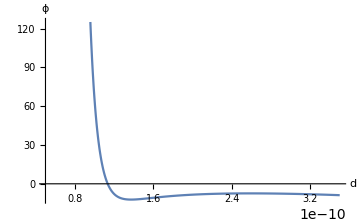

```mathematica
Plot[ϕ[d],{d,0.5*10^(-10),5*10^(-10)},AxesLabel->{"d","ϕ"}]
```

```mathematica
Show[%25,AxesStyle->Gray]
```

-Graphics-

```mathematica
dphi=D[ϕ[d],d]
```

-(1.08864×10^-117)/d^13+(4.9682×10^-19)/d^3-1.16109×10^20 d

```mathematica
ϕ[d]
```

(9.072×10^-119)/d^12+(2.4841×10^-19)/d^2+5.80546×10^19 d^2

Solve::ivar: 1/10000000000 is not a valid variable.

Solve[-(1.08864×10^-117)/d^13+(4.9682×10^-19)/d^3-1.10594×10^20 d==0,d,{1/10000000000,1/5000000000}]

```mathematica
FindMinimum[ϕ[d],{d,10^-10,3 10^-10}]
```

{-12.2504,{d→1.37354×10^-10}}

```mathematica
V2[1.42*10^(-10)]
```

-12.3195

```mathematica
ϕ[1.42*10^(-10)]
```

-12.0848

```mathematica
a = 1.42*10^-10
Subscript[v, p]=1.628009454160189*10^4
Subscript[a, 0] = 5.730674556325455*10^-7
s = 3 √3 a^2/2
Solve[w^2/(2Pi Subscript[v, p]^2)+w/(4Pi Subscript[a, 0])==6/s,w]
```

1.42×10^-10

16280.1

5.73067×10^-7

5.23876×10^-20

{{w→-5.67396×10^14},{w→3.36148×10^14}}

```mathematica
Subscript[T, 1]=(1.05*10^-34)/(1.38*10^-23)3.361477759247811*10^14
```

2557.65

```mathematica
Subscript[w, 2]=√((8*Pi)/s)*7.64*10^3
Subscript[T, 2]=(1.05*10^-34)/(1.38*10^-23)Subscript[w, 2]
```

1.6734×10^14

1273.24

```mathematica
capacity[w_]:=(w^2 Exp[w])/(Exp[w]-1)^2
```

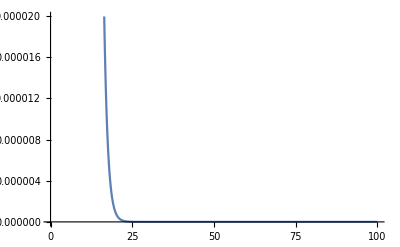

```mathematica
Plot[capacity[w],{w,0.0001,20}]
```

```mathematica
h=QuantityMagnitude[Entity["PhysicalConstant","PlanckConstant"]["Value"]]
e=QuantityMagnitude[Entity["Particle","Electron"]["Charge"]]
```

132521403/200000000000000000000000000000000000000000

-1

```mathematica
Quantity[, "PlanckConstant"]
```

```mathematica
N[Quantity[, "PlanckConstant"]]
```

1. h

```mathematica
UnitConvert[Quantity[1.,"PlanckConstant"],"SI"]
```

4.13567×10^-15 s eV

```mathematica
ClearAll["Global`*"]
ϕ[d_]:=(-B/d^2+(9R)/d^12-5β2*V1^2/B*d^2)
U[d_]
```

U[d_]

```mathematica
dϕ[d_]:=D[D[ϕ[d],d],d]/(4γ)
```

```mathematica
Simplify[dϕ[d]]
```

(-(6 B)/d^4+(1404 R)/d^14-(10 V1^2 β2)/B)/(2 √3)

```mathematica
Simplify[D[dϕ[d],d]*(γ*d^2)/(2γ*d)]
```

(-2 B d^10+378 R)/(d^14 γ)

(2 B)/d^3+(108 R)/d^13-(10 d V1^2 β2)/B

-(2 B)/d^3-(108 R)/d^13+(10 d V1^2 β2)/B

```mathematica
B=(-(6.62607015*10^-34/(2Pi))^2*3.26)/(9.10938356*10^-31)
d = 1.42*10^-10
R=10.08*10^-120*1.602176634*10^-19
V1 = 2.08*1.602176634*10^-19
β2 = 2/3
γ = (√3)/2
(-(6 B)/d^4+(1404 R)/d^14-(10 V1^2 β2)/B)/(2 √3)
```

-3.97998×10^-38

1.42×10^-10

1.61499×10^-138

3.33253×10^-19

2/3

(√3)/2

657.876

```mathematica
Integrate[(e^x x^3)/((e^x-1)^2),{x,0,Infinity}]
```

ConditionalExpression[(6 Zeta[3])/Log[e]^4, Re[Log[e]]<0]

```mathematica
Subscript[k, B]=1.38*10^-23
S=(3 √3(1.42*10^-10)^2)/2*6.02*10^23
Subscript[v, g]=1.62*10^4
hbar=1.0546*10^-34
π^4/15*(Subscript[k, B]^3 S)/(Pi*Subscript[v, g]^2 hbar^2)
```

1.38×10^-23

31537.3

16200.

1.0546×10^-34

0.0000586969

```mathematica
(Subscript[k, B]^2 S)/(4Pi*5.7*10^-7 hbar)*(π^2)/3
```

0.0261571

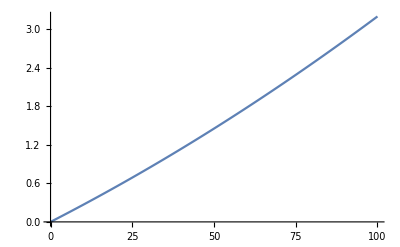

```mathematica
Plot[0.00005869689411205308*x^2+0.026157078950169832*x,{x,0,100}]
```

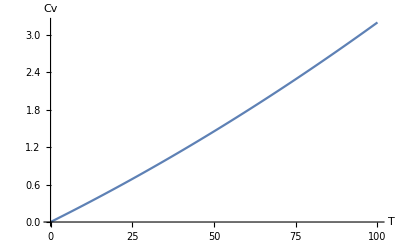

```mathematica
Show[%46,AxesLabel->{HoldForm[T],HoldForm[Cv]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```